### calcular quantas regras existem nos autómatos celulares binário unidimensional de raio 2 quantas regras existem bidimensional binária com vizinhança de von noyman raio 1 descobrir a regra da maioria local de raio 2 unidimensional binária

```mathematica
ArrayPlot[CellularAutomaton[51, RandomInteger[{0,1},100],10],Mesh -> True]
```

-Graphics-

```mathematica
FromDigits[{1,1,0,0,1,1,0,0},2]
```

204

```mathematica
lista = Tuples[{1,0},3]
```

{{1,1,1},{1,1,0},{1,0,1},{1,0,0},{0,1,1},{0,1,0},{0,0,1},{0,0,0}}

```mathematica
{#,1-#[[2]]} &/@Tuples[{1,0},3]
```

{{{1,1,1},0},{{1,1,0},0},{{1,0,1},1},{{1,0,0},1},{{0,1,1},0},{{0,1,0},0},{{0,0,1},1},{{0,0,0},1}}

```mathematica
RnumFromRuleTable[%,2]
```

```mathematica
FromDigits[{#,1-#[[2]]} &/@Tuples[{1,0},3],2]
```

{{240,204,170},51}

```mathematica
Tuples[{1,0},5]
```

{{1,1,1,1,1},{1,1,1,1,0},{1,1,1,0,1},{1,1,1,0,0},{1,1,0,1,1},{1,1,0,1,0},{1,1,0,0,1},{1,1,0,0,0},{1,0,1,1,1},{1,0,1,1,0},{1,0,1,0,1},{1,0,1,0,0},{1,0,0,1,1},{1,0,0,1,0},{1,0,0,0,1},{1,0,0,0,0},{0,1,1,1,1},{0,1,1,1,0},{0,1,1,0,1},{0,1,1,0,0},{0,1,0,1,1},{0,1,0,1,0},{0,1,0,0,1},{0,1,0,0,0},{0,0,1,1,1},{0,0,1,1,0},{0,0,1,0,1},{0,0,1,0,0},{0,0,0,1,1},{0,0,0,1,0},{0,0,0,0,1},{0,0,0,0,0}}

```mathematica
FromDigits[%,2]
```

{4294901760,4278255360,4042322160,3435973836,2863311530}

```mathematica
{#, If[Count[#,1]>Count[#,0],1,0]}&@Tuples[{1,0},5]
```

{{{1,1,1,1,1},{1,1,1,1,0},{1,1,1,0,1},{1,1,1,0,0},{1,1,0,1,1},{1,1,0,1,0},{1,1,0,0,1},{1,1,0,0,0},{1,0,1,1,1},{1,0,1,1,0},{1,0,1,0,1},{1,0,1,0,0},{1,0,0,1,1},{1,0,0,1,0},{1,0,0,0,1},{1,0,0,0,0},{0,1,1,1,1},{0,1,1,1,0},{0,1,1,0,1},{0,1,1,0,0},{0,1,0,1,1},{0,1,0,1,0},{0,1,0,0,1},{0,1,0,0,0},{0,0,1,1,1},{0,0,1,1,0},{0,0,1,0,1},{0,0,1,0,0},{0,0,0,1,1},{0,0,0,1,0},{0,0,0,0,1},{0,0,0,0,0}},0}

```mathematica
FromDigits[{#, If[Count[#,1]>Count[#,0],1,0]}&@Tuples[{1,0},5],2]
```

{{2,2,2,2,2},{2,2,2,2,0},{2,2,2,0,2},{2,2,2,0,0},{2,2,0,2,2},{2,2,0,2,0},{2,2,0,0,2},{2,2,0,0,0},{2,0,2,2,2},{2,0,2,2,0},{2,0,2,0,2},{2,0,2,0,0},{2,0,0,2,2},{2,0,0,2,0},{2,0,0,0,2},{2,0,0,0,0},{0,2,2,2,2},{0,2,2,2,0},{0,2,2,0,2},{0,2,2,0,0},{0,2,0,2,2},{0,2,0,2,0},{0,2,0,0,2},{0,2,0,0,0},{0,0,2,2,2},{0,0,2,2,0},{0,0,2,0,2},{0,0,2,0,0},{0,0,0,2,2},{0,0,0,2,0},{0,0,0,0,2},{0,0,0,0,0}}

```mathematica
ECADynamics[110,LP]
```

Complex

### Exercício 1 em sala dia 18/09/24 -- Contar e agrupar as regras de Lipard

```mathematica
lista = Range[0,255]
```

{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,209,210,211,212,213,214,215,216,217,218,219,220,221,222,223,224,225,226,227,228,229,230,231,232,233,234,235,236,237,238,239,240,241,242,243,244,245,246,247,248,249,250,251,252,253,254,255}

```mathematica
GatherBy[ECADynamics[#,lp]&/@lista,0]
```

{{N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N},{P2,P2,P2,P2,P2,P2,P2,P2,P2,P2,P2,P2,P2,P2,P2,P2,P2,P2,P2,P2,P2,P2,P2,P2,P2,P2,P2,P2},{Fps,Fps,Fps,Fps,Fps,Fps,Fps,Fps,Fps,Fps,Fps,Fps,Fps,Fps,Fps,Fps,Fps,Fps,Fps,Fps,Fps,Fps,Fps,Fps,Fps,Fps,Fps,Fps,Fps,Fps,Fps,Fps,Fps,Fps,Fps,Fps,Fps,Fps,Fps,Fps,Fps,Fps,Fps,Fps,Fps,Fps,Fps,Fps,Fps,Fps,Fps,Fps,Fps,Fps},{P2s,P2s,P2s,P2s,P2s,P2s,P2s,P2s,P2s,P2s,P2s,P2s,P2s,P2s,P2s,P2s,P2s,P2s,P2s,P2s,P2s,P2s,P2s,P2s,P2s,P2s,P2s,P2s,P2s,P2s,P2s,P2s,P2s,P2s,P2s,P2s,P2s,P2s,P2s,P2s,P2s,P2s,P2s,P2s,P2s,P2s,P2s,P2s,P2s,P2s,P2s},{Fp,Fp,Fp,Fp,Fp,Fp,Fp,Fp,Fp,Fp,Fp,Fp,Fp,Fp,Fp,Fp,Fp,Fp,Fp,Fp,Fp,Fp,Fp,Fp,Fp,Fp,Fp,Fp,Fp,Fp,Fp,Fp,Fp,Fp,Fp,Fp,Fp,Fp,Fp,Fp,Fp,Fp,Fp},{Ch,Ch,Ch,Ch,Ch,Ch,Ch,Ch,Ch,Ch,Ch,Ch,Ch,Ch,Ch,Ch,Ch,Ch,Ch,Ch,Ch,Ch,Ch,Ch,Ch,Ch,Ch,Ch,Ch,Ch,Ch,Ch},{Pn,Pn,Pn,Pn,Pn,Pn,Pn,Pn,Pn,Pn,Pn,Pn},{Cplx,Cplx,Cplx,Cplx,Cplx,Cplx},{P3,P3,P3,P3,P3,P3}}

```mathematica
regrasLP={First[#],Length[#]}&/@GatherBy[ECADynamics[#,lp]&/@lista,0]
```

{{N,24},{P2,28},{Fps,54},{P2s,51},{Fp,43},{Ch,32},{Pn,12},{Cplx,6},{P3,6}}

```mathematica
Select[Range[0,255],(ECADynamics[#,lp]=="N")&]
```

{0,8,32,40,64,96,128,136,160,168,192,224,234,235,238,239,248,249,250,251,252,253,254,255}

```mathematica
Module[{par=#},{First[par],Last[par],Select[Range[0,255],(ECADynamics[#,lp]==First[par])&]}]&/@regrasLP // MatrixForm
```

(N | 24 | {0,8,32,40,64,96,128,136,160,168,192,224,234,235,238,239,248,249,250,251,252,253,254,255}
P2 | 28 | {1,5,19,23,25,28,29,33,37,50,51,55,61,67,70,71,91,95,103,108,123,127,156,157,179,198,199,201}
Fps | 54 | {2,10,16,24,34,42,46,48,56,57,58,66,80,98,99,112,114,116,130,138,139,144,152,162,163,170,171,174,175,176,177,184,185,186,187,188,189,190,191,194,208,209,226,227,230,231,240,241,242,243,244,245,246,247}
P2s | 51 | {3,6,7,9,11,14,15,17,20,21,27,31,35,38,39,43,47,49,52,53,59,63,65,74,81,83,84,85,87,88,111,113,115,117,119,125,134,142,143,148,155,158,159,173,178,211,212,213,214,215,229}
Fp | 43 | {4,12,13,36,44,68,69,72,76,77,78,79,92,93,100,104,132,140,141,164,172,196,197,200,202,203,204,205,206,207,216,217,218,219,220,221,222,223,228,232,233,236,237}
Ch | 32 | {18,22,30,45,60,73,75,86,89,90,101,102,105,106,109,120,122,126,129,135,146,149,150,151,153,161,165,169,182,183,195,225}
Pn | 12 | {26,41,82,97,107,121,154,166,167,180,181,210}
Cplx | 6 | {54,110,124,137,147,193}
P3 | 6 | {62,94,118,131,133,145})

### Versão 2

```mathematica
{#,GatherBy[ECADynamics[#,lp] ,0]}&/@lista
```

GatherBy::list: List expected at position 1 in GatherBy[N,0].

GatherBy::list: List expected at position 1 in GatherBy[P2,0].

GatherBy::list: List expected at position 1 in GatherBy[Fps,0].

General::stop: Further output of GatherBy::list will be suppressed during this calculation.

### Exercício 2 - Quantas classes de equivalência dinâmica existe no espaço elementar e quem são

```mathematica
classes =GatherBy[Range[0,255],DynamicalEquivalenceClass[#]&]
```

{{0},{1},{2},{3},{4},{5},{6},{7},{8},{9},{10},{11},{12},{13},{14},{15},{16},{17},{18},{19},{20},{21},{22},{23},{24},{25},{26},{27},{28},{29},{30},{31},{32},{33},{34},{35},{36},{37},{38},{39},{40},{41},{42},{43},{44},{45},{46},{47},{48},{49},{50},{51},{52},{53},{54},{55},{56},{57},{58},{59},{60},{61},{62},{63},{64},{65},{66},{67},{68},{69},{70},{71},{72},{73},{74},{75},{76},{77},{78},{79},{80},{81},{82},{83},{84},{85},{86},{87},{88},{89},{90},{91},{92},{93},{94},{95},{96},{97},{98},{99},{100},{101},{102},{103},{104},{105},{106},{107},{108},{109},{110},{111},{112},{113},{114},{115},{116},{117},{118},{119},{120},{121},{122},{123},{124},{125},{126},{127},{128},{129},{130},{131},{132},{133},{134},{135},{136},{137},{138},{139},{140},{141},{142},{143},{144},{145},{146},{147},{148},{149},{150},{151},{152},{153},{154},{155},{156},{157},{158},{159},{160},{161},{162},{163},{164},{165},{166},{167},{168},{169},{170},{171},{172},{173},{174},{175},{176},{177},{178},{179},{180},{181},{182},{183},{184},{185},{186},{187},{188},{189},{190},{191},{192},{193},{194},{195},{196},{197},{198},{199},{200},{201},{202},{203},{204},{205},{206},{207},{208},{209},{210},{211},{212},{213},{214},{215},{216},{217},{218},{219},{220},{221},{222},{223},{224},{225},{226},{227},{228},{229},{230},{231},{232},{233},{234},{235},{236},{237},{238},{239},{240},{241},{242},{243},{244},{245},{246},{247},{248},{249},{250},{251},{252},{253},{254},{255}}

```mathematica
Length[classes]
```

88

```mathematica
First[#]&/@classes
```

{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,18,19,22,23,24,25,26,27,28,29,30,32,33,34,35,36,37,38,40,41,42,43,44,45,46,50,51,54,56,57,58,60,62,72,73,74,76,77,78,90,94,104,105,106,108,110,122,126,128,130,132,134,136,138,140,142,146,150,152,154,156,160,162,164,168,170,172,178,184,200,204,232}

## Aula dia 25/09

### Shift das regras

#### Esse passo cria a lista ou tabela de transição de estados

```mathematica
shiftD = {#,Last[#]} &/@ Tuples[{1,0},3] // MatrixForm
```

({1,1,1} | 1
{1,1,0} | 0
{1,0,1} | 1
{1,0,0} | 0
{0,1,1} | 1
{0,1,0} | 0
{0,0,1} | 1
{0,0,0} | 0)

#### Essa função gera o número da regra pela lista de transição de estados

```mathematica
RnumFromRuleTable[shiftD,2]
```

2863311530

```mathematica
ArrayPlot[CellularAutomaton[{RnumFromRuleTable[shiftD,2],2,2},RandomInteger[{0,1},100],100]]
```

-Graphics-

```mathematica
shiftD1 = {#,#[[4]]} &/@ Tuples[{1,0},5]
```

{{{1,1,1,1,1},1},{{1,1,1,1,0},1},{{1,1,1,0,1},0},{{1,1,1,0,0},0},{{1,1,0,1,1},1},{{1,1,0,1,0},1},{{1,1,0,0,1},0},{{1,1,0,0,0},0},{{1,0,1,1,1},1},{{1,0,1,1,0},1},{{1,0,1,0,1},0},{{1,0,1,0,0},0},{{1,0,0,1,1},1},{{1,0,0,1,0},1},{{1,0,0,0,1},0},{{1,0,0,0,0},0},{{0,1,1,1,1},1},{{0,1,1,1,0},1},{{0,1,1,0,1},0},{{0,1,1,0,0},0},{{0,1,0,1,1},1},{{0,1,0,1,0},1},{{0,1,0,0,1},0},{{0,1,0,0,0},0},{{0,0,1,1,1},1},{{0,0,1,1,0},1},{{0,0,1,0,1},0},{{0,0,1,0,0},0},{{0,0,0,1,1},1},{{0,0,0,1,0},1},{{0,0,0,0,1},0},{{0,0,0,0,0},0}}

```mathematica
RnumFromRuleTable[shiftD1,2]
```

3435973836

```mathematica
GraphicsRow[{ArrayPlot[CellularAutomaton[{RnumFromRuleTable[shiftD,2],2,2},RandomInteger[{0,1},100],100]],ArrayPlot[CellularAutomaton[{RnumFromRuleTable[shiftD1,2],2,2},RandomInteger[{0,1},100],100]]}]
```

-Graphics-

```mathematica
shiftE = {#,First[#]} &/@ Tuples[{1,0},5]
```

{{{1,1,1,1,1},1},{{1,1,1,1,0},1},{{1,1,1,0,1},1},{{1,1,1,0,0},1},{{1,1,0,1,1},1},{{1,1,0,1,0},1},{{1,1,0,0,1},1},{{1,1,0,0,0},1},{{1,0,1,1,1},1},{{1,0,1,1,0},1},{{1,0,1,0,1},1},{{1,0,1,0,0},1},{{1,0,0,1,1},1},{{1,0,0,1,0},1},{{1,0,0,0,1},1},{{1,0,0,0,0},1},{{0,1,1,1,1},0},{{0,1,1,1,0},0},{{0,1,1,0,1},0},{{0,1,1,0,0},0},{{0,1,0,1,1},0},{{0,1,0,1,0},0},{{0,1,0,0,1},0},{{0,1,0,0,0},0},{{0,0,1,1,1},0},{{0,0,1,1,0},0},{{0,0,1,0,1},0},{{0,0,1,0,0},0},{{0,0,0,1,1},0},{{0,0,0,1,0},0},{{0,0,0,0,1},0},{{0,0,0,0,0},0}}

```mathematica
RnumFromRuleTable[shiftE,2]
```

4294901760

```mathematica
ArrayPlot[CellularAutomaton[{RnumFromRuleTable[shiftE,2],2,2},RandomInteger[{0,1},100],100]]
```

-Graphics-

```mathematica
shiftE1 = {#,#[[2]]} &/@ Tuples[{1,0},5]
```

{{{1,1,1,1,1},1},{{1,1,1,1,0},1},{{1,1,1,0,1},1},{{1,1,1,0,0},1},{{1,1,0,1,1},1},{{1,1,0,1,0},1},{{1,1,0,0,1},1},{{1,1,0,0,0},1},{{1,0,1,1,1},0},{{1,0,1,1,0},0},{{1,0,1,0,1},0},{{1,0,1,0,0},0},{{1,0,0,1,1},0},{{1,0,0,1,0},0},{{1,0,0,0,1},0},{{1,0,0,0,0},0},{{0,1,1,1,1},1},{{0,1,1,1,0},1},{{0,1,1,0,1},1},{{0,1,1,0,0},1},{{0,1,0,1,1},1},{{0,1,0,1,0},1},{{0,1,0,0,1},1},{{0,1,0,0,0},1},{{0,0,1,1,1},0},{{0,0,1,1,0},0},{{0,0,1,0,1},0},{{0,0,1,0,0},0},{{0,0,0,1,1},0},{{0,0,0,1,0},0},{{0,0,0,0,1},0},{{0,0,0,0,0},0}}

```mathematica
RnumFromRuleTable[shiftE,2]
ArrayPlot[CellularAutomaton[{RnumFromRuleTable[shiftE1,2],2,2},RandomInteger[{0,1},100],100]]
```

4294901760

-Graphics-

```mathematica
shiftC = {#,#[[3]]} &/@ Tuples[{1,0},5]
```

{{{1,1,1,1,1},1},{{1,1,1,1,0},1},{{1,1,1,0,1},1},{{1,1,1,0,0},1},{{1,1,0,1,1},0},{{1,1,0,1,0},0},{{1,1,0,0,1},0},{{1,1,0,0,0},0},{{1,0,1,1,1},1},{{1,0,1,1,0},1},{{1,0,1,0,1},1},{{1,0,1,0,0},1},{{1,0,0,1,1},0},{{1,0,0,1,0},0},{{1,0,0,0,1},0},{{1,0,0,0,0},0},{{0,1,1,1,1},1},{{0,1,1,1,0},1},{{0,1,1,0,1},1},{{0,1,1,0,0},1},{{0,1,0,1,1},0},{{0,1,0,1,0},0},{{0,1,0,0,1},0},{{0,1,0,0,0},0},{{0,0,1,1,1},1},{{0,0,1,1,0},1},{{0,0,1,0,1},1},{{0,0,1,0,0},1},{{0,0,0,1,1},0},{{0,0,0,1,0},0},{{0,0,0,0,1},0},{{0,0,0,0,0},0}}

```mathematica
shiftR = {#,If[EvenQ[#[[3]]],1,0]} &/@ Tuples[{1,0},5]
```

{{{1,1,1,1,1},0},{{1,1,1,1,0},0},{{1,1,1,0,1},0},{{1,1,1,0,0},0},{{1,1,0,1,1},1},{{1,1,0,1,0},1},{{1,1,0,0,1},1},{{1,1,0,0,0},1},{{1,0,1,1,1},0},{{1,0,1,1,0},0},{{1,0,1,0,1},0},{{1,0,1,0,0},0},{{1,0,0,1,1},1},{{1,0,0,1,0},1},{{1,0,0,0,1},1},{{1,0,0,0,0},1},{{0,1,1,1,1},0},{{0,1,1,1,0},0},{{0,1,1,0,1},0},{{0,1,1,0,0},0},{{0,1,0,1,1},1},{{0,1,0,1,0},1},{{0,1,0,0,1},1},{{0,1,0,0,0},1},{{0,0,1,1,1},0},{{0,0,1,1,0},0},{{0,0,1,0,1},0},{{0,0,1,0,0},0},{{0,0,0,1,1},1},{{0,0,0,1,0},1},{{0,0,0,0,1},1},{{0,0,0,0,0},1}}

```mathematica
(#+1)&[9]
```

10

```mathematica
GraphicsRow[{ArrayPlot[CellularAutomaton[{RnumFromRuleTable[shiftE,2],2,2},#,100]],ArrayPlot[CellularAutomaton[{RnumFromRuleTable[shiftE1,2],2,2},#,100]],ArrayPlot[CellularAutomaton[{RnumFromRuleTable[shiftC,2],2,2},#,100]],ArrayPlot[CellularAutomaton[{RnumFromRuleTable[shiftR,2],2,2},#,100]],ArrayPlot[CellularAutomaton[{RnumFromRuleTable[shiftD1,2],2,2},#,100]],ArrayPlot[CellularAutomaton[{RnumFromRuleTable[shiftD,2],2,2},#,100]]}]&[RandomInteger[{0,1},100]]
```

-Graphics-

#### Essa regra (232) é a regra da maioria local

```mathematica
RuleTable[232] // MatrixForm
```

({1,1,1} | 1
{1,1,0} | 1
{1,0,1} | 1
{1,0,0} | 0
{0,1,1} | 1
{0,1,0} | 0
{0,0,1} | 0
{0,0,0} | 0)

```mathematica
ArrayPlot[CellularAutomaton[{RnumFromRuleTable[RuleTable[232],2],2,2},RandomInteger[{0,1},100],100]]
```

-Graphics-

#### Regra da minoria local 23 - Essa função RuleTable gera a matriz de estados da regra

```mathematica
RuleTable[23] // MatrixForm
```

({1,1,1} | 0
{1,1,0} | 0
{1,0,1} | 1
{1,0,0} | 0
{0,1,1} | 0
{0,1,0} | 0
{0,0,1} | 0
{0,0,0} | 0)

```mathematica
ArrayPlot[CellularAutomaton[{RnumFromRuleTable[RuleTable[32],2],2,2},RandomInteger[{0,1},100],100]]
```

-Graphics-

#### Essa é a regra que soma a qtde de uns... se der par é 0 ou se der ímpar é 1 --> nome = regra da paridade local (XOR)

```mathematica
RuleTable[150] // MatrixForm
```

({1,1,1} | 1
{1,1,0} | 0
{1,0,1} | 0
{1,0,0} | 1
{0,1,1} | 0
{0,1,0} | 1
{0,0,1} | 1
{0,0,0} | 0)

#### Regra da paridade de zeros ou inversa -- qtde de zeros se der par é 0 se der ímpar é 1 (XNOR)

```mathematica
RuleTable[105] // MatrixForm
```

({1,1,1} | 0
{1,1,0} | 1
{1,0,1} | 1
{1,0,0} | 0
{0,1,1} | 1
{0,1,0} | 0
{0,0,1} | 0
{0,0,0} | 1)

#### Regra Ver detalhe no notebook do professor idem para a regra 77

```mathematica
RuleTable[178] // MatrixForm
```

({1,1,1} | 1
{1,1,0} | 0
{1,0,1} | 1
{1,0,0} | 1
{0,1,1} | 0
{0,1,0} | 0
{0,0,1} | 1
{0,0,0} | 0)

```mathematica
Select[Range[0,255],BFConservativeQ]
```

{}

```mathematica
BFConservativeQ[32]
```

BFConservativeQ[32]

### Verificar se uma regra é conservativa e analisar seu comportamento (Exemplo regra 226 que é conservativa)

```mathematica
BFConservativeQ[226]
RuleTable[226] // MatrixForm
```

```mathematica
regra = CellularAutomaton[{226,2,2},RandomInteger[{0,1},100],100];
ArrayPlot[CellularAutomaton[{226,2,2},RandomInteger[{0,1},100],100]]
```

```mathematica
Total[#] &/@ regra
```

#### Teste do Exercício 3

```mathematica
testRule={{a_,_,_},{a_,_,_},{a_,_,_}}-> If[EvenQ[a],0,1]
```

{{a_,_,_},{a_,_,_},{a_,_,_}}→1

## Aula 02/10/24

#### Gráfico de De Bruijn - Por ele é possível visualizar as imagens e pré-imagens dos steps através das arestas e vértices Ele representa o camportamento da regra em um time step

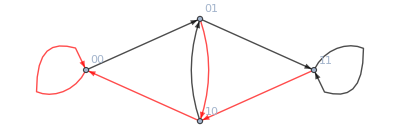

```mathematica
RuleDeBruijnGraph[170,2,1]
```

#### Orfão é o menor bloco que nunca vai aparecer na regra durante a evolução temporal da regra.

#### O comando abaixo é para ver o comportamento das regras - Todas as bacias de atração Parâmetros: regra, estados, vizinhos e quantidade de vizinhos

```mathematica
BAField[110,2,1,5]
```

-Graphics-

#### Bacia de Atração também. Parâmetros: regra, estados, vizinhos e quantidade de vizinhos

```mathematica
BasinsOfAttraction[110,2,1,7]
```

{-Graphics-,-Graphics-}

#### Limite de Ciclos

```mathematica
LimitCycles[BAField[110,2,1,7]]
```

{{{0,0,0,1,0,1,1}->{0,0,1,1,1,1,1},{0,0,1,1,1,1,1}->{0,1,1,0,0,0,1},{0,1,1,0,0,0,1}->{1,1,1,0,0,1,1},{1,1,1,0,0,1,1}->{0,0,1,0,1,1,0},{0,0,1,0,1,1,0}->{0,1,1,1,1,1,0},{0,1,1,1,1,1,0}->{1,1,0,0,0,1,0},{1,1,0,0,0,1,0}->{1,1,0,0,1,1,1},{1,1,0,0,1,1,1}->{0,1,0,1,1,0,0},{0,1,0,1,1,0,0}->{1,1,1,1,1,0,0},{1,1,1,1,1,0,0}->{1,0,0,0,1,0,1},{1,0,0,0,1,0,1}->{1,0,0,1,1,1,1},{1,0,0,1,1,1,1}->{1,0,1,1,0,0,0},{1,0,1,1,0,0,0}->{1,1,1,1,0,0,1},{1,1,1,1,0,0,1}->{0,0,0,1,0,1,1}}}

#### Jardim do Eden (pontos iniciais) configuração que não tem pré-imagem

```mathematica
GoEs[BAField[110,2,1,7]] % // Length
```

49

```mathematica
BAField[150,2,1,6]
```

-Graphics-

## Aula 09/10/24

### 1 - Composição de Regras: a regra 13 2 estados com raio 0.5 com a regra 5 2 estados raio 0.5 composta, fica igual o resultado da regra 187

```mathematica
CompositeRule[{150,1},{150,1},2]  (* {nr regra, raio}, estados*)
```

{2779077210,2,2}

### 2 - Existe um grafo que permite representar tudo que possa obter após n finitos time steps - Basta compor n vezes a mesma regra

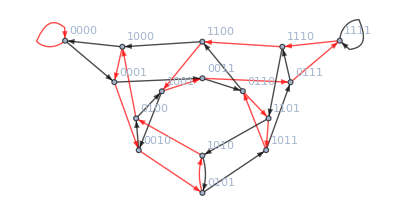

```mathematica
RuleDeBruijnGraph[2779077210,2,2] (* regra, estados, raio*)
```

### 3 - Como encontrar a regra que composta dá ela? usando o decomposeCa

```mathematica
DecomposeCA[{187,2,1},0.5]  (* {regra, estado, raio} raio que quero decompor*)
Map[First[#] &, %%, {2}] (* limpar os estados e raio e junta os par de regras*)
```

{{{5,2,0.5},{4,2,0.5}},{{13,2,0.5},{4,2,0.5}},{{13,2,0.5},{5,2,0.5}},{{11,2,0.5},{10,2,0.5}},{{10,2,0.5},{11,2,0.5}},{{11,2,0.5},{11,2,0.5}}}

{{5,4},{13,4},{13,5},{11,10},{10,11},{11,11}}

#### 4 - Verificar todas as regras do ECA compostas são comutativas ou não comutativas (não trazer as trivias - ela própria)

```mathematica
Module[{regra,lista={}},
For[i=0, i<256, i++, 
For[j=0, j<256, j++, 
regra = If[CompositeRule[{j,1},{i,1},2]==CompositeRule[{i,1},{j,1},2],{i,j}];
Append[lista,regra]]];
lista;
]
```

### REGRA 204 é a Identidade --- Identidade sempre comuta com todas as outras REGRAS 170 e 240 são shift(esquerda e direita) também comutam com todas REGRAS 184 e 226 regra do tráfego (direita/esquerda) as regras 0 e 255 transição dos estados 000 -> e 111 -> 1

```mathematica
RuleTable[204] //MatrixForm
RuleMinDNF[204]
```

({1,1,1} | 1
{1,1,0} | 1
{1,0,1} | 0
{1,0,0} | 0
{0,1,1} | 1
{0,1,0} | 1
{0,0,1} | 0
{0,0,0} | 0)

x_0

#### Regras reversíveis do espaço elementar

```mathematica
Select[Range[0,255],ReversibleRuleQ[#] &]
```

{15,51,85,170,204,240}

```mathematica
CellularAutomaton[30, {{1}, 0}, 50]; (* mesma configuração abaixo porém como é espaço elementar não precisa dos estados e raio*)
ArrayPlot[CellularAutomaton[{30,2,1}, {{1}, 0}, 50]] (* essa configuração é o primeiro {regra, estados, raio} o segundo {configuração inicial} o terceiro timesteps*)
```

-Graphics-

```mathematica
regra90 = Xor[#1, #3] &{{1,0,1}, {1,1,0}, {0,1,1}, {0,1,0}};
(*ArrayPlot[CellularAutomaton[regra90, {{1}, 0}, 50]]*)
Function[viz,viz/. regra90]
```

Function[viz,viz/.regra90]

#### Aula 17/10 Para casa: Parte 1: Verificar no espaço de regras unidimensionais ternárias (3 estados) de raio 1/2 se existe alguma regra estritamente conservativa -- 18683 regras ( Estritamente conservativas são aquelas que preservam o nr de 0,1 e 2 conforme estado inicial) Parte 2: É possível achar alguma no raio 1? Pode usar a versão totalistica -- 2187 {2186,{3,1}}} (nr regra no espaço, (estados e raios))

#### TESTES

```mathematica
contarElementos[lista_]:={Count[lista,0],Count[lista,1],Count[lista,2]}
StrictNumberConservationQ[regra_Integer,estado_Integer, raio_Integar,timesteps_Integer]:= Module[
{automato,estadoInicial,estadoFinal},
automato=CellularAutomaton[{regra,3,1/2},RandomInteger[{0,estado-1},timesteps]; (* {{0,1,2}, 0} Isso é o estado inicial no lugar do ramdom*)
estadoInicial=First[contarElementos/@automato];
estadoFinal=Total[estadoInicial];
AllTrue[automato,Total[#]==estadoFinal&]
]
```

```mathematica
StrictNumberConservationQ[15897,3,1,50]
```

False

```mathematica
lista =Tuples[{0,1,2},RandomInteger[{3,10}]]
est1 = First[contarElementos/@lista]
AllTrue[lista,contarElementos[#]==est1&]
```

{6,0,0}

False

```mathematica
RandomInteger[{0,2},10]
```

{2,1,1,2,2,0,2,0,1,0}

```mathematica
StrictNumberConservationQ[regra_,estados_,raio_]:=Module[{vizinhos,configuracao,listasaidas,outputForConfig,inputStateCounts,outputStateCounts},
vizinhos=2*raio+1;
configuracao=Tuples[Range[0,estados-1],vizinhos];
listasaidas=IntegerDigits[regra,estados,Length[configuracao]];
AllTrue[Range[Length[configuracao]],Function[i,inputStateCounts=Counts[configuracao[[i]]];
outputForConfig=listasaidas[[i]];
outputStateCounts=Counts[Append[configurations[[i,2;;-2]],outputForConfig]];
inputStateCounts==outputStateCounts]]]
```